## Harmonic Oscillator Redux

## Completed and Analyzed in class, April 8, 2025

This is the seventeenth notebook for you to finish in class. We are going to revisit the harmonic oscillator problems we solved back in the fourth and fifth notebooks. This time we are going to let Mathematica do all the hard work!

We are leaving behind the crutch of thinking of continuous systems as chunks. We are going to describe continuous systems as continuous systems, which means imagining the limit that the sizes of the chunks goes to zero while the number of chunks goes to infinity.

But first, we need to get familiar with how Mathematica expects continuous systems to be described. Just as we divided space into chunks, even before that in the course, we began by dividing time into steps and then used Euler’s Method or Second-Order Runge-Kutta to march forward through the discrete steps of time. In reality, probably all the way down to the unfathomably short amount of time (10^-43 seconds)  known as the “Planck time,” time is also continuous.

Let’s see how we describe time-dependent differential equations to Mathematica. Before we get to guitar strings and drumheads, we are going all the way back to the fourth and fifth notebooks, where we solved the damped and driven harmonic oscillator problems.

### Damped Harmonic Oscillator — Refresher

Back in the fourth notebook, we considered this force law:

F=-20x-v

We combined this with Newton’s Law F=ma with m=5 and then we had

5a=-20x-v

Then we got slight fancier and more general. First we divided through by the 5 (whoop-do-doo — one step at a time). We  could also put all the terms on the left:

a+1/5 v+20/5 x=0

The ratio 20/5 is the ratio of the spring constant to the mass and we called that ω_0^2. So for these constants, ω_0=√(20/5)=2. The ratio1/5 is the ratio of the damping coefficient to the mass and we called that combination 2γ. So for these constants 2γ=1/5 or γ=1/10.

Our equation is now:

a+2γv+ω_0^2 x=0

When ω_0>γ as it is here (2 is definitely greater than 1/10), the system is “underdamped.” The greater the ratio of ω_0/γ the more oscillations occur for each  1/e-folding of the envelope of the oscillation as its motion damps toward nothing. We went through all this almost two weeks ago, (in weeks three and four of the semester) and I am giving you a quick refresher, and it is ok if you don’t remember all the results, because now we want to rediscover them, but by forcing Mathematica to do the hard work of breaking time into steps and applying some numerical solver.

### Derivatives and Their Notation

We have one more step, which is to introduce the notation of derivatives. We can’t tell Mathematica what to do if we don’t have a precise notation.

Recall that the velocity v is the rate of change (with respect to time) of the position x. Meanwhile the acceleration a is the rate of change (with respect to time) of the velocity v. The rate of change is called the derivative. To say that you want to take a derivative of x(t) with respect to t in Mathematica, you write:

```mathematica
Derivative[1][x][t];
```

Perhaps it is a bit clumsy, and indeed there are shorthands, but let us understand this form, because it is unambiguous and it is general which makes it powerful.

Derivative[1][x][t] says take one derivative of the function x with respect to its argument, and evaluate the resulting function at time t.

So far we haven’t done anything at all with our symbolic expression of the derivative. One thing we can do with it is just display it in a pretty form:

```mathematica
Derivative[1][x][t] // TraditionalForm
```

x'(t)

The afterthought of TraditionalForm says that you would like to see the result as it would be likely to be typeset in a mathematics textbook or in some physics textbooks. Note that physicists (and older mathematicians) often use a different notation for the derivatives. The notation is known as Leibniz notation. We have our hands full learning Mathematica’s notations. Let’s not add Leibniz notation into the mix we are already considering in this notebook.

The acceleration is the rate of change of the velocity, and that is the second derivative, and here is how you tell Mathematica you want to take a second derivative of x with respect to t:

```mathematica
Derivative[2][x][t] // TraditionalForm
```

x''(t)

### The Damped Oscillator Differential Equation

Here is how you write the whole damped oscillator equation (which if you scroll up, you will see we had whittled down to a+2γv+ω_0^2 x=0) in a way that Mathematica can unambiguously understand it, and as an afterthought, display it prettily:

```mathematica
Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0 // TraditionalForm
```

2 gamma x'(t)+omega0^2 x(t)+x''(t)==0

Equations involving derivatives are called “differential equations.”

Notice with your full attention the use of == rather than = in the differential equation. We are not making an assignment! We are setting up a conditional test between two sides of an equation, and Mathematica is going to do its best to approximately satisfy that conditional test when (deep under the hood) it applies some differential-equation solving strategy like Euler, or Runge-Kutta Second Order, or maybe Runge-Kutta Fourth Order. (BTW, I apologize that I never got around to introducing Runge-Kutta Fourth Order as promised early in the course. It is a mess, even for me, and Runge-Kutta Second Order has been serving us fully satisfactorily.)

Now let’s also define omega0 and gamma for Mathematica, and also add some initial conditions on the position and velocity. Since we learned the Module notation recently, I’ll toss that in:

```mathematica
Module[{omega0=2, gamma=1/10},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0,x[0]==0,Derivative[1][x][0]==3}] // TraditionalForm
```

{x''(t)+(x'(t))/5+4 x(t)==0,x(0)==0,x'(0)==3}

I set the initial position at t=0 as 0 and I set the initial velocity as 3. Again, it is extremely important to use == rather than = in the initial conditions as well as in the differential equation. We are setting up conditional tests and Mathematica is going to work to make them true. If you screw that up and put in assignments, it is quit and restart time.

We have failed to do one minor thing. We have set up a pile of equations, but we haven’t given them any name, so we can’t use them anywhere else without typing them in again.

Let’s give this pile of equations a name:

```mathematica
dampedOscillatorProblem=Module[{omega0=2, gamma=1/10},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0,x[0]==0,Derivative[1][x][0]==3}] ;
```

### Making Mathematica Do The Hard Work

This particular problem is exactly solvable. So you can tell Mathematica to try to exactly solve it using DSolve, and lo and behold, it succeeds:

```mathematica
DSolve[dampedOscillatorProblem]
```

{{x[t]→10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]}}

Notice that what is output is a list of lists of rules. All that generality is in case you have multiple functions being solved simultaneously. We just have one function, so we grab the first and only list of rules out of the list of lists of rules:

```mathematica
dampedOscillatorSolutionRule = DSolve[dampedOscillatorProblem][[1]];
```

Display it so that we can see exactly what we got:

```mathematica
dampedOscillatorSolutionRule
```

{x[t]→10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]}

We still don’t have something we can plot, because you don’t plot a rule. We have to turn the rule into a function, and we do that by first writing x[t] and then applying the rule to it:

```mathematica
x[t]/.dampedOscillatorSolutionRule
```

10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]

It doesn’t take much space to write x[t]/.dampedOscillatorSolutionRule, but we can be even slicker and define a new function:

```mathematica
dampedOscillatorSolution[t_]=x[t]/.dampedOscillatorSolutionRule

dampedOscillatorSolution[t]
```

10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]

10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]

To be frank, I don’t know why I might or might not use := above instead of =. I am following 
https://reference.wolfram.com/language/howto/SolveADifferentialEquation.html.en, and in that documentation they don’t use := so I am not. Here is a screenshot of the relevant portion of the documentation:

-Graphics-

### Plotting Damped Harmonic Motion

Finally, we plot the solution:

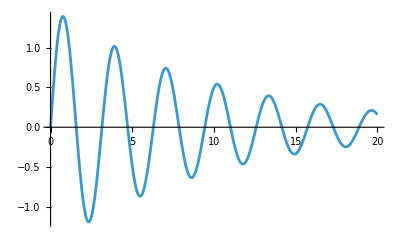

```mathematica
Plot[dampedOscillatorSolution[t],{t,0,20}]
```

### Animating Damped Harmonic Motion

```mathematica
oscillatorGraphic[displacement_]:=Graphics[{
EdgeForm[Thin],White,
Rectangle[{-2.0,-1.0},{2.0,1.0}],
Black,
Point[{0,0}],
Point[{displacement,0}]
}]
oscillatorGraphic[1.0]
```

-Graphics-

```mathematica
Animate[oscillatorGraphic[dampedOscillatorSolution[t]],{t, 0, 20},DefaultDuration->20]
```